```mathematica
SetDirectory[NotebookDirectory[]];Get["include/Perturbation_Theory.m"];Get["include/Pauli_Elem_Representation.m"];Get["include/Plotting_Definitions.m"];
```

```mathematica
Eff=({{E0, 0, 0, 0}, {0, E1, 0, 0}, {0, 0, E2, 0}, {0, 0, 0, E3}});Ecav=({{0, 0}, {0, wc}});Zff=({{0, z31, 0, 0}, {z31, 0, 0, 0}, {0, 0, 0, -z31}, {0, 0, -z31, 0}})+({{0, 0, z10, 0}, {0, 0, 0, z10}, {z10, 0, 0, 0}, {0, z10, 0, 0}});
ZffNoise=({{0, 0, 0, z11-z22}, {0, 0, z11+z22, 0}, {0, z11+z22, 0, 0}, {z11-z22, 0, 0, 0}});
a=({{0, 1}, {0, 0}});adag=({{0, 0}, {1, 0}});
Hff=KroneckerProduct[IdentityMatrix[2],Eff,IdentityMatrix[4]]+KroneckerProduct[IdentityMatrix[2],IdentityMatrix[4],Eff];
Hcav=KroneckerProduct[Ecav,IdentityMatrix[4],IdentityMatrix[4]];
Hint=1/2 g*KroneckerProduct[(a+adag),IdentityMatrix[4],IdentityMatrix[4]].(KroneckerProduct[IdentityMatrix[2],IdentityMatrix[4]+Zff,IdentityMatrix[4]]+KroneckerProduct[IdentityMatrix[2],IdentityMatrix[4],IdentityMatrix[4]+Zff]);
H=Hff+Hcav+Hint;
```

```mathematica
Sub={E0-> -22.622179872/2,E1-> -11.484289055+22.622179872/2,E2-> -11.168261874+22.622179872/2,E3-> -0.028128942+22.622179872/2,g-> 0.1,wc->10,z10-> 9.95205331*^-01,z31-> 9.53351183*^-02,wrms->0.323}
```

{E0→-11.3111,E1→-0.173199,E2→0.142828,E3→11.283,g→0.1,wc→10,z10→0.995205,z31→0.0953351,wrms→0.323}

```mathematica
hn1=1/2 wrms*KroneckerProduct[IdentityMatrix[2],ZffNoise,IdentityMatrix[4]];
hn2=1/2 wrms*KroneckerProduct[IdentityMatrix[2],IdentityMatrix[4],ZffNoise];
```

```mathematica
populatedStates={1,4,16}+1;
allStates=Table[i,{i,32}];
remainingStates=DeleteCases[allStates,Alternatives@@populatedStates]
reorderedStates=Join[populatedStates,remainingStates]
```

{1,3,4,6,7,8,9,10,11,12,13,14,15,16,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

{2,5,17,1,3,4,6,7,8,9,10,11,12,13,14,15,16,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

```mathematica
H0=Diagonal[H[[reorderedStates,reorderedStates]]];
V=H[[reorderedStates,reorderedStates]]-DiagonalMatrix[H0];
```

```mathematica
( HSW=SWTransH[H0,V,3,2]+DiagonalMatrix[H0[[1;;3]]])//MatrixForm
```

(E0+E1+1/2 (-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc))) | (g^2 z31^2)/(4 (E0-E1-wc)) | (g z31)/2
(g^2 z31^2)/(4 (E0-E1-wc)) | E0+E1+1/2 (-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc))) | (g z31)/2
(g z31)/2 | (g z31)/2 | 2 E0+wc+1/2 ((2 g^2)/wc+(g^2 z10^2)/(E0-E2+wc)))

```mathematica
hn1[[reorderedStates,reorderedStates]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11+z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 wrms (z11-z22) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[HSW]
```

{-1/(4 (E0-E2-wc) wc (-E1+E3+wc))(-4 E0 E1 g^2+4 E1 E2 g^2+4 E0 E3 g^2-4 E2 E3 g^2+4 E0^2 E1 wc+4 E0 E1^2 wc-4 E0 E1 E2 wc-4 E1^2 E2 wc-4 E0^2 E3 wc-4 E0 E1 E3 wc+4 E0 E2 E3 wc+4 E1 E2 E3 wc+13+4 E1 E2 wc^2+4 E0 E3 wc^2+4 E1 E3 wc^2-4 g^2 wc^2+4 E0 wc^3+4 E1 wc^3+E0 g^2 wc z10^2+E1 g^2 wc z10^2-E2 g^2 wc z10^2-E3 g^2 wc z10^2-2 g^2 wc^2 z10^2),(-12 E0^4 E1 wc+131)/(8 (E0-E1-wc) (E0-E2-wc) wc (E0-E2+wc) (-E1+E3+wc)),(-12 E0^4 E1 wc+8 E0^3 E1^2 wc+128+√((135+2 g^2 1 z31^2)^2-4 (-16 E0^6 E1^2 g^4+2784)))/(8 (E0-E1-wc) (E0-E2-wc) wc (E0-E2+wc) (-E1+E3+wc))}
 |  |  |  |

```mathematica
%//Simplify
```

{(4 E1^2 wc (E2+wc)+4 E0^2 wc (-E1+E3+wc)+g^2 (4 E2 E3+2 wc^2 (2+z10^2)+E2 wc (4+z10^2)+E3 wc (4+z10^2))-E0 (4 E1^2 wc+4 E3 (g^2+wc (E2+wc))-4 E1 (g^2+wc (E2+E3+2 wc))+wc (4 wc (E2+wc)+g^2 (4+z10^2)))-E1 (4 E2 (g^2+wc (E3+wc))+wc (4 wc (E3+wc)+g^2 (4+z10^2))))/(4 (E0-E2-wc) wc (-E1+E3+wc)),-(-12 E0^4 E1 wc+131)/(8 (E0-E1-wc) (E0-E2-wc) (E1-E3-wc) wc (E0-E2+wc)),-(-12 E0^4 E1 wc+8 E0^3 E1^2 wc+4 E0^2 E1^3 wc+127+√(16 E0^8 wc^2 (-E1+E3+wc)^2+19+E0^2 (32 E1^6 (3 E2^2 wc^2-wc^4)+14)))/(8 (E0-E1-wc) (E0-E2-wc) (E1-E3-wc) wc (E0-E2+wc))}
 |  |  |  |

```mathematica
temp=SWTransH[Diagonal[HSW],HSW-DiagonalMatrix[Diagonal[HSW]],2,2]+DiagonalMatrix[Diagonal[HSW][[1;;2]]]//MatrixForm
```

(E0+E1-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc))+1/2 ((2 g^2)/wc-(g^2 z10^2)/(2 (E0-E2-wc))-(g^2 z10^2)/(2 (E1-E3-wc))-(g^2 z31^2)/(2 (E0-E1-wc)))+(g^2 z31^2)/(4 (-E0+E1-wc+1/2 (-(2 g^2)/wc-(g^2 z10^2)/(E0-E2+wc))+1/2 (-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc))))) | (g^2 z31^2)/(4 (E0-E1-wc))+(g^2 z31^2)/(4 (-E0+E1-wc+1/2 (-(2 g^2)/wc-(g^2 z10^2)/(E0-E2+wc))+1/2 (-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc)))))
(g^2 z31^2)/(4 (E0-E1-wc))+(g^2 z31^2)/(4 (-E0+E1-wc+1/2 (-(2 g^2)/wc-(g^2 z10^2)/(E0-E2+wc))+1/2 (-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc))))) | E0+E1-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc))+1/2 ((2 g^2)/wc-(g^2 z10^2)/(2 (E0-E2-wc))-(g^2 z10^2)/(2 (E1-E3-wc))-(g^2 z31^2)/(2 (E0-E1-wc)))+(g^2 z31^2)/(4 (-E0+E1-wc+1/2 (-(2 g^2)/wc-(g^2 z10^2)/(E0-E2+wc))+1/2 (-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc))))))

```mathematica
Diagonal[HSW]
```

{E0+E1+1/2 (-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc))),E0+E1+1/2 (-(2 g^2)/wc+(g^2 z10^2)/(2 (E0-E2-wc))+(g^2 z10^2)/(2 (E1-E3-wc))+(g^2 z31^2)/(2 (E0-E1-wc))),2 E0+wc+1/2 ((2 g^2)/wc+(g^2 z10^2)/(E0-E2+wc))}

```mathematica
HSW-DiagonalMatrix[Diagonal[HSW]]//Simplify//MatrixForm
```

(0 | (g^2 z31^2)/(4 E0-4 E1-4 wc) | (g z31)/2
(g^2 z31^2)/(4 E0-4 E1-4 wc) | 0 | (g z31)/2
(g z31)/2 | (g z31)/2 | 0)

```mathematica
temp[[1,1,1]]-temp[[1,2,2]]//Simplify
```

0

```mathematica
(g^2 z31^2)/(4 (E0-E1-wc))+(g^2 z31^2)/(4 (-E0+E1-wc+1/2 (-(2 g^2)/wc-(g^2 z10^2)/(E0-E2+wc))+1/2 (-(2 g^2)/wc+(g^2 z10^2)/(E0-E2-wc)+(g^2 z31^2)/(2 (E0-E1-wc)))))//Simplify
```

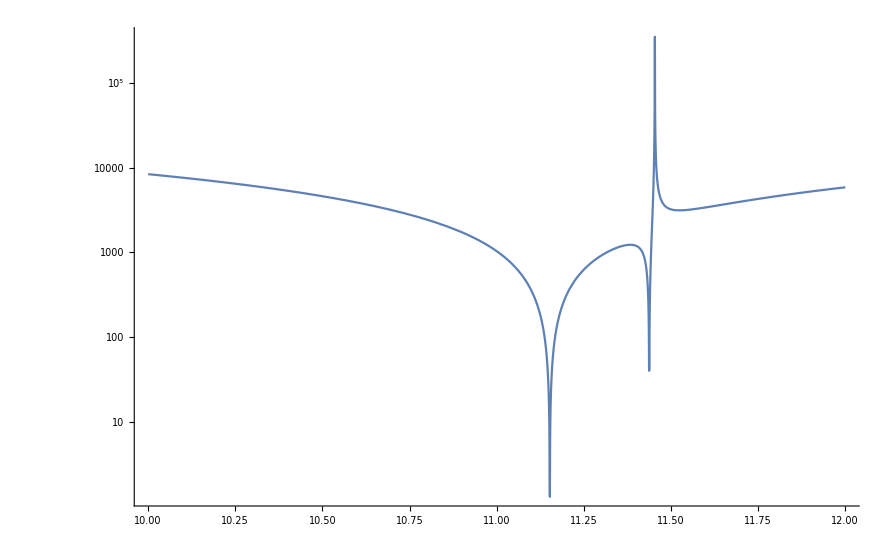

```mathematica
LogPlot[1/Abs[2*π*1/4 g^2 z31^2 (1/(E0-E1-wc)+4/(-4 E0+4 E1-(8 g^2)/wc-4 wc+(2 g^2 z10^2)/(E0-E2-wc)-(2 g^2 z10^2)/(E0-E2+wc)+(g^2 z31^2)/(E0-E1-wc)))//.{wc->x}//.Sub],{x,10,12},PlotRange->All]
```

```mathematica
List@@(-(8 g^2)/wc+(2 g^2 z10^2)/(E0-E2-wc)-(2 g^2 z10^2)/(E0-E2+wc))//.Sub
```

{-0.008,-0.000923313,0.0136243}

```mathematica
E2-E0//.Sub
E1-E0//.Sub
```

11.4539

11.1379